## Constant Values

```mathematica
obh2=0.022383;
orh2=4.184*10^(-5);
omh2=0.143140;
```

## D.E. for Linear Matter Perturbations

```mathematica
smoothsgn[z_,zs_,ee_]:=Tanh[(zs-z)/ee];
Hlcdm[z_,om_]:=Sqrt[om (1+z)^3+(1-om)];
Hlscdm[z_,om_,zs_,ee_]:=Sqrt[om (1+z)^3+(1-om) smoothsgn[z,zs,ee]];

amin=1/1000;

dsol1[om_?NumberQ]:=(dsol1[om]=Module[{a},NDSolve[{-((3 om d1[a] Hlcdm[0,om]^2)/(2 a^5  Hlcdm[1/a-1,om]^2))+d1'[a] (3/a+D[Hlcdm[1/a-1,om],a]/Hlcdm[1/a-1,om])+d1''[a]==0,d1[amin]==0.002126029525092128,d1'[amin]==2.126029525092128},d1,{a,amin,1}][[1]]])
(* The growth rate and fσ8 - LCDM *)
Da1[a_?NumberQ,om_?NumberQ]:=d1[a]/.dsol1[om]
fa1[aa_,om_]:=a d1'[a]/d1[a]/.a->aa/.dsol1[om]
fσ81[a_?NumberQ,om_?NumberQ,σ8_?NumberQ]:=(σ8 Da1[aa,om])/Da1[1,om] fa1[aa,om]/.aa->a
dsol[om_?NumberQ,zs_?NumberQ,ee_?NumberQ]:=(dsol[om,zs,ee]=Module[{a},NDSolve[{-((3 om d[a] Hlscdm[0,om,zs,ee]^2)/(2 a^5  Hlscdm[1/a-1,om,zs,ee]^2))+d'[a] (3/a+D[Hlscdm[1/a-1,om,zs,ee],a]/Hlscdm[1/a-1,om,zs,ee])+d''[a]==0,d[amin]==0.0020845141040286164,d'[amin]==2.0845141040286164},d,{a,amin,1}][[1]]])
(* The growth rate and fσ8 *)
Da[a_?NumberQ,om_?NumberQ,zs_?NumberQ,ee_?NumberQ]:=d[a]/.dsol[om,zs,ee]
fa[aa_,om_,zs_,ee_]:=a d'[a]/d[a]/.a->aa/.dsol[om,zs,ee]
fσ8[a_?NumberQ,om_?NumberQ,zs_?NumberQ,ee_?NumberQ,σ8_?NumberQ]:=(σ8 Da[aa,om,zs,ee])/Da[1,om,zs,ee] fa[aa,om,zs,ee]/.aa->a
fσ8z[z_?NumberQ,om_?NumberQ,zs_?NumberQ,ee_?NumberQ,σ8_?NumberQ]:=(σ8 Da[aa,om,zs,ee])/Da[1,om,zs,ee] fa[aa,om,zs,ee]/.aa->1/(1+z)
fσ8zLCDM[a_?NumberQ,om_?NumberQ,σ8_?NumberQ]:=(σ8 Da1[aa,om])/Da1[1,om] fa1[aa,om]/.aa->1/(1+z)
```

## Importing Data

```mathematica
(* Import the Robust Growth Data from https://arxiv.org/pdf/1806.10822.pdf*)
(* Please use correct path for the data files *)
datagrowth=Import["C:\\Users\\camar\\Documents\\programs\\MDP-Ls\\data\\fs8_2018.txt","Table"];
dataSDSS=Import["C:\\Users\\camar\\Documents\\programs\\MDP-Ls\\data\\SDSS.txt","Table"];
dataWiggleZ=Import["C:\\Users\\camar\\Documents\\programs\\MDP-Ls\\data\\WiggleZ.txt","Table"];
```

```mathematica
dchi[nsig_]:=2 InverseGammaRegularized[M/2,1-Erf[nsig/(√2)]]/.M->2//N
nsig[dchi1_]:=FindRoot[dchi[nsig1]==dchi1,{nsig1,1}][[1,2]]
dchi2[nsig_]:=2 InverseGammaRegularized[M/2,1-Erf[nsig/(√2)]]/.M->2//N
nsig2[dchi1_]:=FindRoot[dchi2[nsig1]==dchi1,{nsig1,3}][[1,2]]
deltachi2[nsig_,m_]:=2 InverseGammaRegularized[m/2,1-Erf[nsig/(√2)]]
CijWiggleZ=({{0.00640, 0.002570, 0.000000}, {0.00257, 0.003969, 0.002540}, {0.00000, 0.002540, 0.005184}});
CijSDSS=({{0.030975999999999997, 0.0089176032, 0.0032857439999999997, -0.00021081279999999997}, {0.0089176032, 0.009801, 0.004357584000000001, 0.0007576668}, {0.003285744, 0.004357584000000001, 0.004900000000000001, 0.003502982000000001}, {-0.00021081279999999997, 0.0007576668, 0.0035029820000000004, 0.011236}});

invcijwiggle=Inverse[CijWiggleZ];
invcijsdss=Inverse[CijSDSS];
(*   **************************************   *)

Cijfs81=DiagonalMatrix[datagrowth[[All,3]]^2];
InvCijfs81=Inverse[Cijfs81];

(* χ^2 correlated term ΛCDM*)
vecgr1[data_,om_,σ8_]:=Table[data[[i,2]]-fσ81[1/(1+data[[i,1]]),om,σ8],{i,1,Length[data]}]
chi2corr1wigglez[data_,om_,σ8_]:=vecgr1[data,om,σ8].invcijwiggle.vecgr1[data,om,σ8]
chi2corr1unc[data_,om_,σ8_]:=vecgr1[data,om,σ8].InvCijfs81.vecgr1[data,om,σ8]
chi2corr1sdss[data_,om_,σ8_]:=vecgr1[data,om,σ8].invcijsdss.vecgr1[data,om,σ8]
chi2lcdm[om_,σ8_]:=chi2corr1unc[datagrowth,om,σ8]+chi2corr1sdss[dataSDSS,om,σ8]+chi2corr1wigglez[dataWiggleZ,om,σ8]
```

```mathematica
(* χ^2 correlated term ΛsCDM *)
vecgr[data_,zs_,ee_,om_,σ8_]:=Table[data[[i,2]]-fσ8[1/(1+data[[i,1]]),om,zs,ee,σ8],{i,1,Length[data]}]
chi2corrunc[data_,zs_,ee_,om_,σ8_]:=vecgr[data,zs,ee,om,σ8].InvCijfs81.vecgr[data,zs,ee,om,σ8]
chi2corrwigglez[data_,zs_,ee_,om_,σ8_]:=vecgr[data,zs,ee,om,σ8].invcijwiggle.vecgr[data,zs,ee,om,σ8]
chi2corrsdss[data_,zs_,ee_,om_,σ8_]:=vecgr[data,zs,ee,om,σ8].invcijsdss.vecgr[data,zs,ee,om,σ8]
chi2lscdm[om_,σ8_]:=chi2corrunc[datagrowth,1.7,0.001,om,σ8]+chi2corrsdss[dataSDSS,1.7,0.001,om,σ8]+chi2corrwigglez[dataWiggleZ,1.7,0.001,om,σ8]
```

```mathematica
(* Minimize χ^2 over different parameters *)
fmwc5=FindMinimum[chi2lscdm[om,σ8],{om,.3,.31},{σ8,.8,.81}];
FindMinimum[chi2lscdm[om,σ8],{om,0.3,0.31},{σ8,0.8,0.81}];
fmlcdm=FindMinimum[chi2lcdm[om,σ8],{om,.3,.31},{σ8,.8,.81}];
```

```mathematica
omblcdm=fmlcdm[[2,1,2]];
σ8lcdm=fmlcdm[[2,2,2]];
ombfwc5=fmwc5[[2,1,2]];
σ8bfwc5=fmwc5[[2,2,2]];
```

```mathematica
(* Growth contours for LsCDM with zs=1.5 *)
contcpl122=ContourPlot[chi2lscdm[om,σ8],{om,0.1,0.6},{σ8,0.5,1.2},Contours->{fmwc5[[1]]+deltachi2[1,2],fmwc5[[1]]+deltachi2[2,2]},
ContourShading->{Cyan,RGBColor[0.78,1,0.96], White}];
(* Growth contours for LCDM *)
contlcdm0=ContourPlot[chi2lcdm[om,σ8],{om,0.1,0.6},{σ8,0.5,1.2},Contours->{fmlcdm[[1]]+deltachi2[1,2],fmlcdm[[1]]+deltachi2[2,2]},ContourShading->{Cyan,RGBColor[0.78,1,0.96], White}];
contlcdm1=ContourPlot[chi2lcdm[om,σ8],{om,0.1,0.6},{σ8,0.5,1.2},Contours->{fmlcdm[[1]]+deltachi2[1,2],fmlcdm[[1]]+deltachi2[2,2]},ContourShading->None,ContourStyle->{{Gray,Dashed},{Gray,Dashed}}];
```

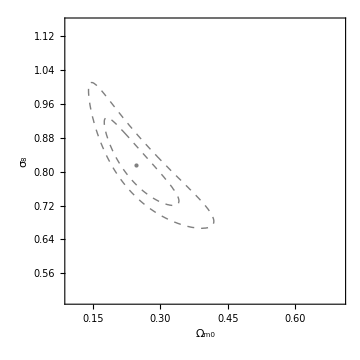

```mathematica
contLCDM1=Show[{contlcdm1},Epilog->{{PointSize[Medium],Gray,Point[{omblcdm,σ8lcdm}]}},FrameLabel->{"\!\(\*SubscriptBox[\(Ω\), \(m0\)]\)","\!\(\*SubscriptBox[\(σ\), \(8\)]\)"},PlotRange->{{0.1,0.7},{0.5,1.15}},PlotRangeClipping->True,BaseStyle->{FontFamily->"Times",18},FrameStyle->Directive[Black],ImageSize->Medium]
```

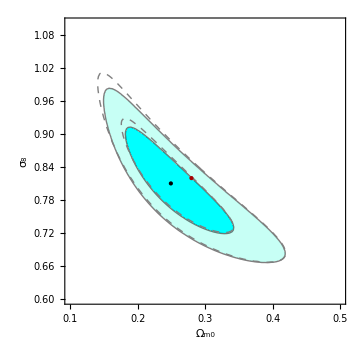

```mathematica
PlotLsCDM=Show[{contcpl122,contLCDM1},Epilog->{{PointSize[Medium],Black,Point[{ombfwc5,σ8bfwc5}]},{PointSize[Large],Darker[Red],Point[{0.2796,0.8191}]}},FrameLabel->{"\!\(\*SubscriptBox[\(Ω\), \(m0\)]\)","\!\(\*SubscriptBox[\(σ\), \(8\)]\)"},PlotRange->{{0.1,0.5},{0.6,1.1}},PlotRangeClipping->True,BaseStyle->{FontFamily->"Times",30},FrameStyle->Directive[Black],ImageSize->Medium]
```

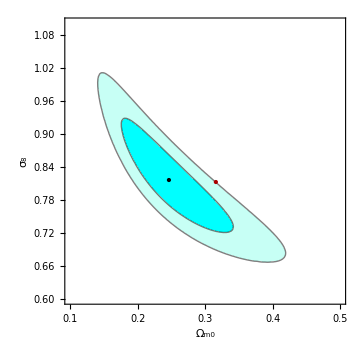

```mathematica
contLCDM=Show[{contlcdm0},Epilog->{{PointSize[Medium],Black,Point[{omblcdm,σ8lcdm}]},{PointSize[Large],Darker[Red],Point[{0.3158,0.8120}]}},FrameLabel->{"\!\(\*SubscriptBox[\(Ω\), \(m0\)]\)","\!\(\*SubscriptBox[\(σ\), \(8\)]\)"},PlotRange->{{0.1,0.5},{0.6,1.1}},PlotRangeClipping->True,BaseStyle->{FontFamily->"Times",30},FrameStyle->Directive[Black],ImageSize->Medium]
```

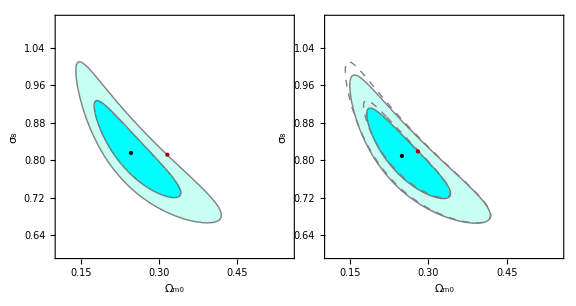

```mathematica
fsize=50;
contou1b=Show[contLCDM,Frame->{{True,True},{True,True}},PlotRange->{{0.11,0.55},{0.6,1.1}},LabelStyle->{25}];
contou2b=Show[{PlotLsCDM},Frame->{{False,True},{True,True}},PlotRange->{{0.11,0.55},{0.6,1.1}},LabelStyle->{25}];

figure01=GraphicsGrid[{{contou1b,contou2b}},Spacings->-43.65,ImageSize->Large]
```

```mathematica
(* 1-σ distance for 2D parameter space*)
```

```mathematica
N[deltachi2[1,2]]
```

2.29575

```mathematica
(*σ - Distance for LCDM*)
chi2lcdm[omblcdm,σ8lcdm]-chi2lcdm[0.3163,0.8136]
```

-6.60098

```mathematica
(*σ - Distance for LsCDM*)
chi2lscdm[ombfwc5,σ8bfwc5]-chi2lscdm[0.2796,0.8191]
```

-2.21498

## Errors for Λ_sCDM:

```mathematica
chifun01=ListInterpolation[ParallelTable[chi2lscdm[om,σ8],{om,ombfwc5-0.01,ombfwc5+0.01,0.01},{σ8,σ8bfwc5-0.01,σ8bfwc5+0.01,0.01},DistributedContexts->Automatic],{{ombfwc5-0.01,ombfwc5+0.01},{σ8bfwc5-0.01,σ8bfwc5+0.01}}];
(* Params that we want to calculate the errors *)
params={om,σ8}
(* Calculation of the 1σ error according to Eq.(15.3.5) from Numerical Recipes *)
Fij=1/2 Table[D[chifun01[om,σ8],params[[p]],params[[d]]]/.fmwc5[[2]],{p,1,Length[params]},{d,1,Length[params]}];
cij=Inverse[Fij];
errors=Sqrt[Diagonal[cij]]
Print["The best fit parameters for Ω_(0  m) and σ_8 are: Ω_(0  m)=",NumberForm[ombfwc5,3]," ± ",NumberForm[errors[[1]],1], " and σ_8=",NumberForm[σ8bfwc5,3]," ± ",NumberForm[errors[[2]],1]," respectively."]

Fij//MatrixForm
cij//MatrixForm
errors//MatrixForm
```

ListInterpolation::inhr: Requested order is too high; order has been reduced to {2,2}.

{om,σ8}

{0.0521678,0.0638276}

(1655.8 | 1193.76
1193.76 | 1106.1)

(0.00272148 | -0.00293714
-0.00293714 | 0.00407397)

(0.0521678
0.0638276)

The best fit parameters for Ω_(0  m) and σ_8 are: Ω_(0  m)=0.249 ± 0.05 and σ_8=0.809 ± 0.06 respectively.

The best fit parameters for Ω_(0  m) and σ_8 are: Ω_(0  m)=0.249 ± 0.05 and σ_8=0.809 ± 0.06 respectively.

## Errors for ΛCDM:

```mathematica
chifun02=ListInterpolation[ParallelTable[chi2lcdm[om,σ8],{om,omblcdm-0.01,omblcdm+0.01,0.01},{σ8,σ8lcdm-0.01,σ8lcdm+0.01,0.01},DistributedContexts->Automatic],{{omblcdm-0.01,omblcdm+0.01},{σ8lcdm-0.01,σ8lcdm+0.01}}];
(* Params that we want to calculate the errors *)
params={om,σ8}
(* Calculation of the 1σ error according to Eq.(15.3.5) from Numerical Recipes *)
Fij=1/2 Table[D[chifun02[om,σ8],params[[p]],params[[d]]]/.fmlcdm[[2]],{p,1,Length[params]},{d,1,Length[params]}];
cij=Inverse[Fij];
errors=Sqrt[Diagonal[cij]]
Print["The best fit parameters for Ω_(0  m) and σ_8 are: Ω_(0  m)=",NumberForm[omblcdm,3]," ± ",NumberForm[errors[[1]],1], " and σ_8=",NumberForm[σ8lcdm,3]," ± ",NumberForm[errors[[2]],1]," respectively."]

Fij//MatrixForm
cij//MatrixForm
errors//MatrixForm
```

ListInterpolation::inhr: Requested order is too high; order has been reduced to {2,2}.

{om,σ8}

{0.0539404,0.0679518}

The best fit parameters for Ω_(0  m) and σ_8 are: Ω_(0  m)=0.246 ± 0.05 and σ_8=0.816 ± 0.07 respectively.

(1728.01 | 1227.73
1227.73 | 1088.86)

(0.00290957 | -0.00328065
-0.00328065 | 0.00461745)

(0.0539404
0.0679518)

### Error Propagation and S_8= σ_8 (Ω_m0/0.3) ^1/2:

### ΛCDM:

```mathematica
sigmaomlcdm=0.05394017474295068;
sigmaσ8lcdm=0.06795181194381326;
covxylcdm=-0.0032806348145100815;
omlcdm=omblcdm;
S8lcdm=σ8lcdm √(omlcdm/0.3)
sigmaS8lcdm=√(omlcdm/0.3 sigmaomlcdm^2+sigmaσ8lcdm^2((1/2)/(√0.3))^2 omlcdm^-1+2 σ8lcdm/(√0.3)covxylcdm √(omlcdm/0.3)1/2 omlcdm^(-1/2))
```

0.738997

0.0953607

## Λ_sCDM:

```mathematica
sigmaomlscdm=0.05216780712677205;
sigmaσ8lscdm=0.0638276445119847;
covxylscdm=-0.002937142421327166;
omlscdm=ombfwc5;
σ8lscdm=σ8bfwc5;

S8lscdm=σ8lscdm √(omlscdm/0.3)
sigmaS8lscdm=√(omlscdm/0.3 sigmaomlscdm^2+sigmaσ8lscdm^2((1/2)/(√0.3))^2 omlscdm^-1+2 σ8lscdm/(√0.3)covxylscdm √(omlscdm/0.3)1/2 omlscdm^(-1/2))
```

0.737641

0.0892305